```mathematica
(*Zad 1*)
Clear[x]
f[x_]:=Sin[x^2+2x-5]
g[x_]:=f'[x]
```

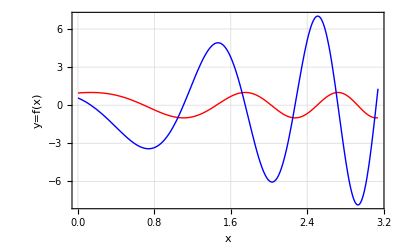

```mathematica
Plot[{f[x],g[x]},{x,0,Pi}, PlotStyle-> {{Red, Thick},{Blue,Thick}},  AxesLabel-> {"x","y=f(x)"}, Frame->True, GridLines->Automatic]
```

```mathematica
(*Zad 2*)
Program[lista_,n_]:=Module[{wystapienia=0},
For [it = 1,  it≤Length[lista],it++,
If[lista[[it]]≥ n,wystapienia++];
];
Return [wystapienia];
];
```

```mathematica
list={6,3,2,4,6,2,1,3,4,9,0,2,4,15,23,6,15,12,3,12,512,512,3,123,125,12,51232,123,562,34,268,45,5,345,5234};
```

```mathematica
Program[list,6]
```

22

```mathematica
(*Zad 3*)
Program2[macierz_,n_]:=Module[{iloczyn=1},
If[Length[macierz]<n, Return ["Błąd"]];
For[wiersz=1,wiersz≤Length[macierz],wiersz++,
iloczyn=iloczyn*macierz[[wiersz,n]];
];
Return[iloczyn];
];
```

```mathematica
mac={{1,2,3},{4,5,6},{7,8,9}};
```

```mathematica
Program2[mac,2]
```

80